## 1 D Toy Model

### Fill Hamiltonian Matrix

```mathematica
N0=20;
kmax=1.;
δk=kmax/N0;
α=1/δk; (* Somewhat arbitrary choice *)

Kinetic=Table[i^2 KroneckerDelta[i,j],{i,-kmax,kmax,δk},{j,-kmax,kmax,δk}];
Potential=Table[δk α/(Abs[i-j]+δk),{i,-kmax,kmax,δk},{j,-kmax,kmax,δk}];
kTab=Table[i,{i,-kmax,kmax,δk}];
```

```mathematica
Dimensions[Kinetic]
```

{41,41}

```mathematica
kTab
```

{-1.,-0.95,-0.9,-0.85,-0.8,-0.75,-0.7,-0.65,-0.6,-0.55,-0.5,-0.45,-0.4,-0.35,-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

### Solve Eigenvalue Problem

```mathematica
{evals,evecs}=Transpose[Sort[Transpose[Eigensystem[Kinetic+Potential]]]];
```

### Plot Solutions

#### Simplistic plots

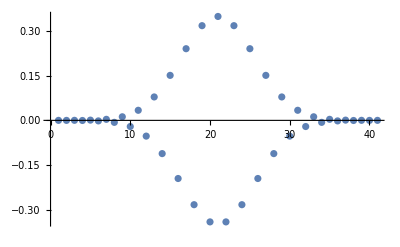

```mathematica
ListPlot[{evecs[[1]](*,evecs[[2]]*)}]
```

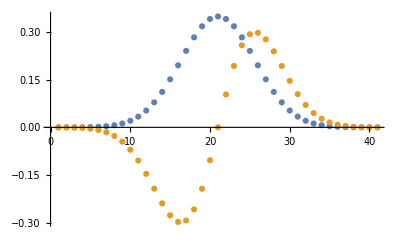

```mathematica
ListPlot[{evecs[[1]]Sign[evecs[[1]]],evecs[[2]]Sign[evecs[[1]]]}]
```

#### Nice plots

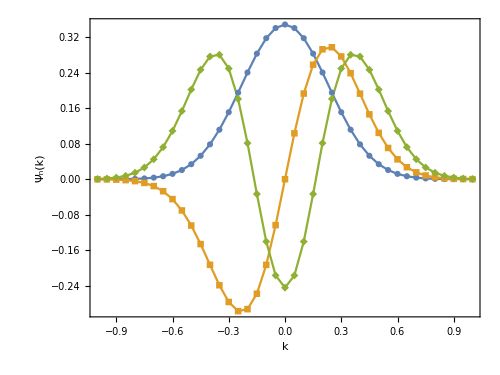

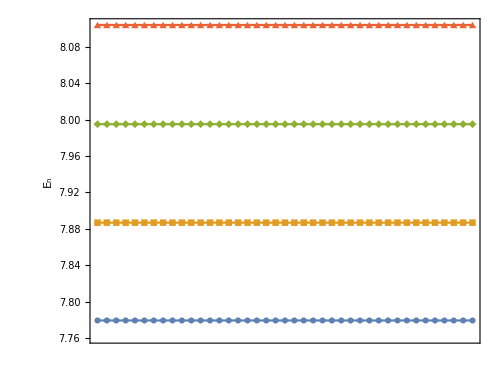

```mathematica
Ψ0=Table[{kTab[[i]],Abs[evecs[[1,i]]]},{i,Length[kTab]}];
 Ψ1=Table[{kTab[[i]],evecs[[2,i]]Sign[evecs[[1,i]]]},{i,Length[kTab]}];
 Ψ2=Table[{kTab[[i]],evecs[[3,i]]Sign[evecs[[1,i]]]},{i,Length[kTab]}];

 E0=Table[{kTab[[i]],evals[[1]]},{i,Length[kTab]}];
 E1=Table[{kTab[[i]],evals[[2]]},{i,Length[kTab]}];
 E2=Table[{kTab[[i]],evals[[3]]},{i,Length[kTab]}];
 E3=Table[{kTab[[i]],evals[[4]]},{i,Length[kTab]}];

ListPlot[{Ψ0,Ψ1,Ψ2},Joined->True,PlotMarkers->Automatic,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{24,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large]

ListPlot[{E0,E1,E2,E3},Joined->True,PlotMarkers->Automatic,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{None,Style["E_n",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,LabelStyle->{24,"ComputerModern",Black},AspectRatio->0.75,FrameTicks->{None,Automatic} (*This line hides x-axis ticks*)]
```

## 2 D Toy Model

### Make 2D k-Grid

```mathematica
N0=18;
kmax=0.5;
δk=kmax/N0;


kGrid=Flatten[ParallelTable[{kx,ky},{kx,-kmax,kmax,δk},{ky,-kmax,kmax,δk}],1];
Dimensions[kGrid]
```

{1369,2}

### Fill Hamiltonian Matrix

```mathematica
Kinetic=ParallelTable[ki.ki KroneckerDelta[ki[[1]],kj[[1]]]KroneckerDelta[ki[[2]],kj[[2]]],{ki,kGrid},{kj,kGrid}];
Potential=ParallelTable[1./(Norm[ki-kj]+δk),{ki,kGrid},{kj,kGrid}];
```

```mathematica
Kinetic//Dimensions
```

{1369,1369}

### Solve Eigenvalue Problem

```mathematica
{evals,evecs}=Transpose[Sort[Transpose[Eigensystem[Kinetic+Potential]]]];
```

### Plot Solutions

#### Simplistic plots

```mathematica
evecs[[1]]
```

{5.06076×10^-10,1.35468×10^-9,-2.04561×10^-8,-2.41423×10^-8,5.15459×10^-7,-5.26474×10^-7,-5.45515×10^-6,0.0000199877,-0.0000289788,0.0000199877,-5.45515×10^-6,-5.26474×10^-7,5.15459×10^-7,-2.41423×10^-8,-2.04561×10^-8,1.35468×10^-9,5.06075×10^-10,1.35468×10^-9,-2.54473×10^-8,1.18538×10^-8,8.56431×10^-7,-2.97179×10^-6,-6.78296×10^-6,0.0000658095,-0.000177096,0.000240479,-0.000177096,0.0000658095,-6.78296×10^-6,-2.97179×10^-6,8.56431×10^-7,1.18538×10^-8,-2.54473×10^-8,1.35468×10^-9,-2.04561×10^-8,1.18538×10^-8,9.82148×10^-7,-5.30487×10^-6,-2.32648×10^-6,0.000121487,-0.000532923,0.00117831,-0.00152067,0.00117831,-0.000532923,0.000121487,-2.32648×10^-6,-5.30487×10^-6,9.82148×10^-7,1.18538×10^-8,-2.04561×10^-8,-2.41423×10^-8,8.56431×10^-7,-5.30487×10^-6,1.21631×10^-6,0.000153847,-0.000960992,0.00306858,-0.00597786,0.00743988,-0.00597786,0.00306858,-0.000960992,0.000153847,1.21631×10^-6,-5.30487×10^-6,8.56431×10^-7,-2.41423×10^-8,5.15459×10^-7,-2.97179×10^-6,-2.32648×10^-6,0.000153847,-0.00115492,0.00481003,-0.0128653,0.023025,-0.0279288,0.023025,-0.0128653,0.00481003,-0.00115492,0.000153847,-2.32648×10^-6,-2.97179×10^-6,5.15459×10^-7,-5.26474×10^-7,-6.78296×10^-6,0.000121487,-0.000960992,0.00481003,-0.0164689,0.039503,-0.0667809,0.0795686,-0.0667809,0.039503,-0.0164689,0.00481003,-0.000960992,0.000121487,-6.78296×10^-6,-5.26474×10^-7,-5.45515×10^-6,0.0000658095,-0.000532923,0.00306858,-0.0128653,0.039503,-0.0886115,0.14439,-0.170027,0.14439,-0.0886115,0.039503,-0.0128653,0.00306858,-0.000532923,0.0000658095,-5.45515×10^-6,0.0000199877,-0.000177096,0.00117831,-0.00597786,0.023025,-0.0667809,0.14439,-0.230459,0.269569,-0.230459,0.14439,-0.0667809,0.023025,-0.00597786,0.00117831,-0.000177096,0.0000199877,-0.0000289788,0.000240479,-0.00152067,0.00743988,-0.0279288,0.0795686,-0.170027,0.269569,-0.314631,0.269569,-0.170027,0.0795686,-0.0279288,0.00743988,-0.00152067,0.000240479,-0.0000289788,0.0000199877,-0.000177096,0.00117831,-0.00597786,0.023025,-0.0667809,0.14439,-0.230459,0.269569,-0.230459,0.14439,-0.0667809,0.023025,-0.00597786,0.00117831,-0.000177096,0.0000199877,-5.45515×10^-6,0.0000658095,-0.000532923,0.00306858,-0.0128653,0.039503,-0.0886115,0.14439,-0.170027,0.14439,-0.0886115,0.039503,-0.0128653,0.00306858,-0.000532923,0.0000658095,-5.45515×10^-6,-5.26474×10^-7,-6.78296×10^-6,0.000121487,-0.000960992,0.00481003,-0.0164689,0.039503,-0.0667809,0.0795686,-0.0667809,0.039503,-0.0164689,0.00481003,-0.000960992,0.000121487,-6.78296×10^-6,-5.26474×10^-7,5.15459×10^-7,-2.97179×10^-6,-2.32648×10^-6,0.000153847,-0.00115492,0.00481003,-0.0128653,0.023025,-0.0279288,0.023025,-0.0128653,0.00481003,-0.00115492,0.000153847,-2.32648×10^-6,-2.97179×10^-6,5.15459×10^-7,-2.41423×10^-8,8.56431×10^-7,-5.30487×10^-6,1.21631×10^-6,0.000153847,-0.000960992,0.00306858,-0.00597786,0.00743988,-0.00597786,0.00306858,-0.000960992,0.000153847,1.21631×10^-6,-5.30487×10^-6,8.56431×10^-7,-2.41423×10^-8,-2.04561×10^-8,1.18538×10^-8,9.82148×10^-7,-5.30487×10^-6,-2.32648×10^-6,0.000121487,-0.000532923,0.00117831,-0.00152067,0.00117831,-0.000532923,0.000121487,-2.32648×10^-6,-5.30487×10^-6,9.82148×10^-7,1.18538×10^-8,-2.04561×10^-8,1.35468×10^-9,-2.54473×10^-8,1.18538×10^-8,8.56431×10^-7,-2.97179×10^-6,-6.78296×10^-6,0.0000658095,-0.000177096,0.000240479,-0.000177096,0.0000658095,-6.78296×10^-6,-2.97179×10^-6,8.56431×10^-7,1.18538×10^-8,-2.54473×10^-8,1.35468×10^-9,5.06075×10^-10,1.35468×10^-9,-2.04561×10^-8,-2.41423×10^-8,5.15459×10^-7,-5.26474×10^-7,-5.45515×10^-6,0.0000199877,-0.0000289788,0.0000199877,-5.45515×10^-6,-5.26474×10^-7,5.15459×10^-7,-2.41423×10^-8,-2.04561×10^-8,1.35468×10^-9,5.06075×10^-10}

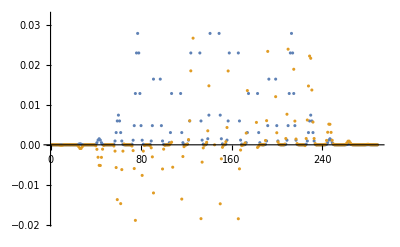

```mathematica
ListPlot[{evecs[[1]]Sign[evecs[[1]]],evecs[[2]]Sign[evecs[[1]]]}]
```

#### Nice plots

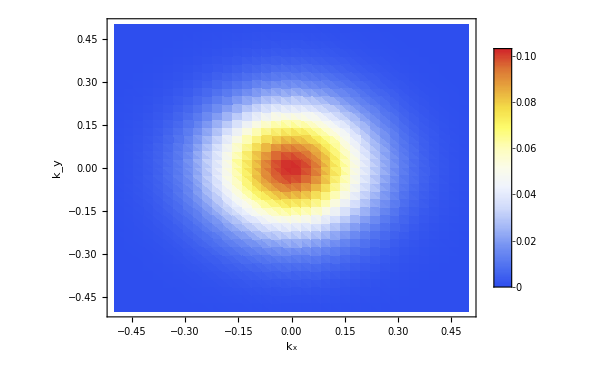

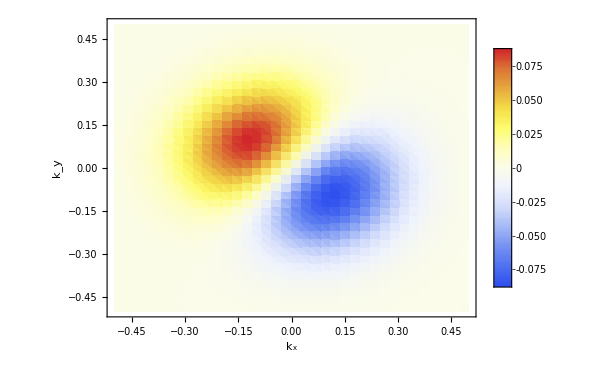

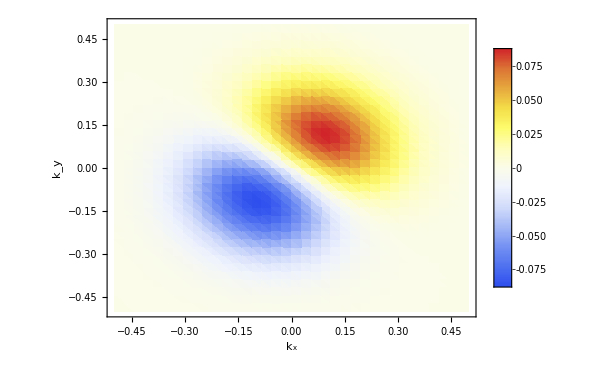

```mathematica
Ψ0=ParallelTable[{kGrid[[i,1]],kGrid[[i,2]],Abs[evecs[[1,i]]]},{i,Length[kGrid]}];
 Ψ1=ParallelTable[{kGrid[[i,1]],kGrid[[i,2]],evecs[[2,i]]Sign[evecs[[1,i]]]},{i,Length[kGrid]}];
Ψ2=ParallelTable[{kGrid[[i,1]],kGrid[[i,2]],evecs[[3,i]]Sign[evecs[[1,i]]]},{i,Length[kGrid]}];
Ψ3=ParallelTable[{kGrid[[i,1]],kGrid[[i,2]],evecs[[4,i]]Sign[evecs[[1,i]]]},{i,Length[kGrid]}];
Ψ4=ParallelTable[{kGrid[[i,1]],kGrid[[i,2]],evecs[[5,i]]Sign[evecs[[1,i]]]},{i,Length[kGrid]}];


ListDensityPlot[Ψ0,ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k_x",24,Black,"ComputerModern"],Style["k_y",24,Black,"ComputerModern"],Style["Ψ_0(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Right]]

ListDensityPlot[Ψ1,ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k_x",24,Black,"ComputerModern"],Style["k_y",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Right]]

ListDensityPlot[Ψ2,ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k_x",24,Black,"ComputerModern"],Style["k_y",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Right]]

ListDensityPlot[Ψ3,ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k_x",24,Black,"ComputerModern"],Style["k_y",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Right]];

ListDensityPlot[Ψ4,ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["k_x",24,Black,"ComputerModern"],Style["k_y",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large,ColorFunction->"TemperatureMap",PlotLegends->Placed[Automatic,Right]];
```

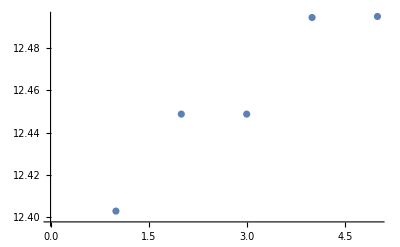

```mathematica
ListPlot[evals[[1;;5]]]
```

```mathematica
(* Comment: I have now labelled/indexed it such that n=0 is the ground state *)
```

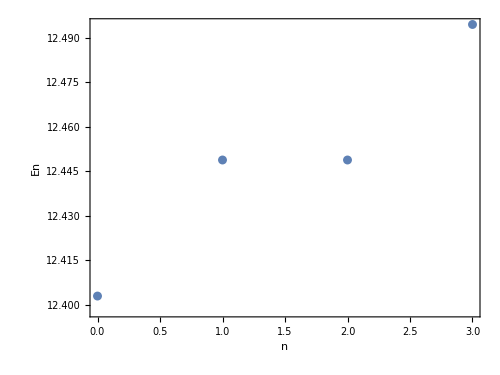

```mathematica
ListPlot[Table[{i-1,evals[[i]]},{i,1,4}],ImageSize->500,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameLabel->{Style["n",24,Black,"ComputerModern"],Style["En",24,Black,"ComputerModern"],Style["Ψ_n(k)",24,Black,"ComputerModern"]},Axes->True,AxesStyle->Black,FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{20,"ComputerModern",Black},AspectRatio->0.75,ImageSize->Large]
```